```mathematica
ClearAll["Global`*"]
deltaT=Symbol["ΔT"];
bulkBC={q'[0]==0,q[R]==0};
eqn = q''[r] + (1/r)*q'[r] - q[r]/((m^2)*l^2) == -λ*deltaT/(((m^2)*l^2)*L)
bulkSol = DSolve[{eqn, bulkBC},q[r],r]
```

-q[r]/(l^2 m^2)+q'[r]/r+q''[r]==-(ΔT λ)/(l^2 L m^2)

{{q[r]→-(ΔT λ (BesselJ[0,(ⅈ r)/(l m)]-BesselJ[0,(ⅈ R)/(l m)]))/(L BesselJ[0,(ⅈ R)/(l m)])}}

```mathematica
qBulk = q[r] /. bulkSol[[1]]
firstOrderSlip = q'[r]/. D[bulkSol[[1]], r] /. r-> R
qWall = -C*l*firstOrderSlip

qTotal = qBulk + qWall
```

-(ΔT λ (BesselJ[0,(ⅈ r)/(l m)]-BesselJ[0,(ⅈ R)/(l m)]))/(L BesselJ[0,(ⅈ R)/(l m)])

(ⅈ ΔT λ BesselJ[1,(ⅈ R)/(l m)])/(l L m BesselJ[0,(ⅈ R)/(l m)])

-(ⅈ C ΔT λ BesselJ[1,(ⅈ R)/(l m)])/(L m BesselJ[0,(ⅈ R)/(l m)])

-(ΔT λ (BesselJ[0,(ⅈ r)/(l m)]-BesselJ[0,(ⅈ R)/(l m)]))/(L BesselJ[0,(ⅈ R)/(l m)])-(ⅈ C ΔT λ BesselJ[1,(ⅈ R)/(l m)])/(L m BesselJ[0,(ⅈ R)/(l m)])

```mathematica
netHeatFlux = Integrate[qTotal*2*π*r, {r, 0, R}]/(π*(R^2)*(deltaT/L))
KnHeatFlux = netHeatFlux /. R -> l/Kn // Simplify
```

(λ (R+((-2 l m^2+C R) BesselI[1,R/(l m)])/(m BesselI[0,R/(l m)])))/R

λ+((C-2 Kn m^2) λ BesselI[1,1/(Kn m)])/(m BesselI[0,1/(Kn m)])

```mathematica
modBoundaryConditions={q'[0]==0,q[R]==-C*l*q'[R]};
eqn = q''[r] + (1/r)*q'[r] - q[r]/((m^2)*l^2) == -λ*deltaT/(((m^2)*l^2)*L)
modBCsol = DSolve[{eqn, modBoundaryConditions},q[r],r]

qTotalModBC = q[r] /. modBCsol[[1]]
```

-q[r]/(l^2 m^2)+q'[r]/r+q''[r]==-(ΔT λ)/(l^2 L m^2)

{{q[r]→-(ΔT λ (m BesselJ[0,(ⅈ r)/(l m)]-m BesselJ[0,(ⅈ R)/(l m)]+ⅈ C BesselJ[1,(ⅈ R)/(l m)]))/(L (m BesselJ[0,(ⅈ R)/(l m)]-ⅈ C BesselJ[1,(ⅈ R)/(l m)]))}}

-(ΔT λ (m BesselJ[0,(ⅈ r)/(l m)]-m BesselJ[0,(ⅈ R)/(l m)]+ⅈ C BesselJ[1,(ⅈ R)/(l m)]))/(L (m BesselJ[0,(ⅈ R)/(l m)]-ⅈ C BesselJ[1,(ⅈ R)/(l m)]))

```mathematica
modBCnetHeatFlux = Integrate[qTotalModBC*2*π*r, {r, 0, R}]/(π*(R^2)*(deltaT/L))
modKnHeatFlux = modBCnetHeatFlux /. R -> l/Kn // Simplify
```

(L λ (m R BesselI[0,R/(l m)]+(-2 l m^2+C R) BesselI[1,R/(l m)]))/(R (L m BesselI[0,R/(l m)]+C L BesselI[1,R/(l m)]))

(λ (m BesselI[0,1/(Kn m)]+(C-2 Kn m^2) BesselI[1,1/(Kn m)]))/(m BesselI[0,1/(Kn m)]+C BesselI[1,1/(Kn m)])

```mathematica
(* Second Order Boundary Condition *)
SOBoundaryConditions={q'[0]==0,q[R]==-C*l*q'[R] + α*l*l*q''[R]};
eqn = q''[r] + (1/r)*q'[r] - q[r]/((m^2)*l^2) == -λ*deltaT/(((m^2)*l^2)*L)
SOBBCsol = DSolve[{eqn, SOBoundaryConditions},q[r],r]
qTotalSO = q[r] /. SOBBCsol[[1]]
```

-q[r]/(l^2 m^2)+q'[r]/r+q''[r]==-(ΔT λ)/(l^2 L m^2)

{{q[r]→-(ΔT λ (m^2 R BesselJ[0,(ⅈ r)/(l m)]-m^2 R BesselJ[0,(ⅈ R)/(l m)]+R α BesselJ[0,(ⅈ R)/(l m)]+ⅈ C m R BesselJ[1,(ⅈ R)/(l m)]+ⅈ l m α BesselJ[1,(ⅈ R)/(l m)]))/(L (m^2 R BesselJ[0,(ⅈ R)/(l m)]-R α BesselJ[0,(ⅈ R)/(l m)]-ⅈ C m R BesselJ[1,(ⅈ R)/(l m)]-ⅈ l m α BesselJ[1,(ⅈ R)/(l m)]))}}

-(ΔT λ (m^2 R BesselJ[0,(ⅈ r)/(l m)]-m^2 R BesselJ[0,(ⅈ R)/(l m)]+R α BesselJ[0,(ⅈ R)/(l m)]+ⅈ C m R BesselJ[1,(ⅈ R)/(l m)]+ⅈ l m α BesselJ[1,(ⅈ R)/(l m)]))/(L (m^2 R BesselJ[0,(ⅈ R)/(l m)]-R α BesselJ[0,(ⅈ R)/(l m)]-ⅈ C m R BesselJ[1,(ⅈ R)/(l m)]-ⅈ l m α BesselJ[1,(ⅈ R)/(l m)]))

```mathematica
SOHeatFlux = Integrate[qTotalSO*2*π*r, {r, 0, R}]/(π*(R^2)*(deltaT/L))
SOKnHeatFlux = SOHeatFlux /. R -> l/Kn // Simplify
```

(L λ (R (m^2-α) BesselI[0,R/(l m)]+m (C R+l (-2 m^2+α)) BesselI[1,R/(l m)]))/(L R (m^2-α) BesselI[0,R/(l m)]+L m (C R+l α) BesselI[1,R/(l m)])

(λ ((m^2-α) BesselI[0,1/(Kn m)]+m (C+Kn (-2 m^2+α)) BesselI[1,1/(Kn m)]))/((m^2-α) BesselI[0,1/(Kn m)]+m (C+Kn α) BesselI[1,1/(Kn m)])

```mathematica
(*Actual Jou Data*)
ClearAll[K, λ, m, l, α, α1]
thermalCondRatio = 1 - 2*Kn*((BesselJ[1, I /Kn]/BesselJ[0, I/ Kn])^2)*((BesselJ[0, I /Kn]/(I*BesselJ[1, I / Kn])) +  K)
condJou = λ(1 - 2*Kn*((BesselJ[1, I /Kn]/BesselJ[0, I/ Kn])^2)*((BesselJ[0, I /Kn]/(I*BesselJ[1, I / Kn])) +  K))
```

1-(2 Kn (K-(ⅈ BesselJ[0,ⅈ/Kn])/BesselJ[1,ⅈ/Kn]) BesselJ[1,ⅈ/Kn]^2)/BesselJ[0,ⅈ/Kn]^2

λ (1-(2 Kn (K-(ⅈ BesselJ[0,ⅈ/Kn])/BesselJ[1,ⅈ/Kn]) BesselJ[1,ⅈ/Kn]^2)/BesselJ[0,ⅈ/Kn]^2)

```mathematica
(* Plotting Stuff *)
modKnHeatFluxPlt = modKnHeatFlux /. C -> K
KnHeatFluxPlt = KnHeatFlux /. C -> K
SOKnHeatFluxPlt = SOKnHeatFlux /. C -> K
SOKnHeatFluxPlt2 = SOKnHeatFlux /. C -> K
SOKnHeatFluxPlt2 = SOKnHeatFluxPlt2 /. α -> α1
```

(λ (m BesselI[0,1/(Kn m)]+(K-2 Kn m^2) BesselI[1,1/(Kn m)]))/(m BesselI[0,1/(Kn m)]+K BesselI[1,1/(Kn m)])

λ+((K-2 Kn m^2) λ BesselI[1,1/(Kn m)])/(m BesselI[0,1/(Kn m)])

(λ ((m^2-α) BesselI[0,1/(Kn m)]+m (K+Kn (-2 m^2+α)) BesselI[1,1/(Kn m)]))/((m^2-α) BesselI[0,1/(Kn m)]+m (K+Kn α) BesselI[1,1/(Kn m)])

(λ ((m^2-α) BesselI[0,1/(Kn m)]+m (K+Kn (-2 m^2+α)) BesselI[1,1/(Kn m)]))/((m^2-α) BesselI[0,1/(Kn m)]+m (K+Kn α) BesselI[1,1/(Kn m)])

(λ ((m^2-α1) BesselI[0,1/(Kn m)]+m (K+Kn (-2 m^2+α1)) BesselI[1,1/(Kn m)]))/((m^2-α1) BesselI[0,1/(Kn m)]+m (K+Kn α1) BesselI[1,1/(Kn m)])

```mathematica
λ = 1;
K = 1;
m = 1;
α = 2/9;
α1 = 1/2;
```

```mathematica
(*Plot[modKnHeatFluxPlt, {Kn, 0, 10}]*)
```

```mathematica
(*Plot[KnHeatFluxPlt, {Kn, 0, 10}]*)
```

General::munfl: 1/(0.+4.71020785901165×10^2123 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

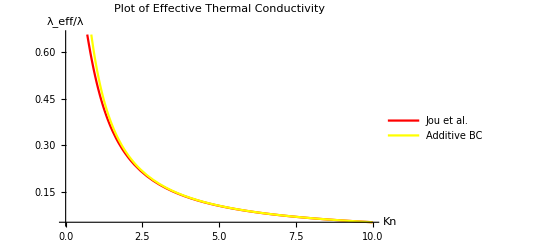

```mathematica
Plot[{thermalCondRatio, KnHeatFluxPlt(*, modKnHeatFluxPlt, SOKnHeatFluxPlt, SOKnHeatFluxPlt2*)},{Kn,0,10},PlotLegends->{"Jou et al.","Additive BC" , "First Order BC", "SO BC α = 2
9",  "SO BC α = 1
2"},PlotStyle->{Red,Yellow, Green, Purple, Blue},AxesLabel->{"Kn","λ_eff/λ"},PlotLabel->"Plot of Effective Thermal Conductivity"]
```

```mathematica
(*Conductivity Dependance on R*)
ClearAll[K, λ, m, l, Kmod, KJou, mNet, Kso, α, α1]
condPltNetHeatFlux = netHeatFlux /. C -> K /. R-> d/2
condPltModNetHeatFlux = modBCnetHeatFlux/. C-> Kmod  /. Kn -> l/R /. R -> d/2
condPltJou = condJou /. Kn -> l/R /. R-> d/2;
condPltJou = condPltJou /. K -> KJou
condPltSOHeatFlux = SOHeatFlux /. C -> Kso /. R-> d/2
condPltSOHeatFlux1 = SOHeatFlux /. C -> Kso /. α -> α1 /. R-> d/2
```

(2 λ (d/2+(((d K)/2-2 l m^2) BesselI[1,d/(2 l m)])/(m BesselI[0,d/(2 l m)])))/d

(2 L λ (1/2 d m BesselI[0,d/(2 l m)]+((d Kmod)/2-2 l m^2) BesselI[1,d/(2 l m)]))/(d (L m BesselI[0,d/(2 l m)]+Kmod L BesselI[1,d/(2 l m)]))

λ (1-(4 l (KJou-(ⅈ BesselJ[0,(ⅈ d)/(2 l)])/BesselJ[1,(ⅈ d)/(2 l)]) BesselJ[1,(ⅈ d)/(2 l)]^2)/(d BesselJ[0,(ⅈ d)/(2 l)]^2))

(L λ (1/2 d (m^2-α) BesselI[0,d/(2 l m)]+m ((d Kso)/2+l (-2 m^2+α)) BesselI[1,d/(2 l m)]))/(1/2 d L (m^2-α) BesselI[0,d/(2 l m)]+L m ((d Kso)/2+l α) BesselI[1,d/(2 l m)])

(L λ (1/2 d (m^2-α1) BesselI[0,d/(2 l m)]+m ((d Kso)/2+l (-2 m^2+α1)) BesselI[1,d/(2 l m)]))/(1/2 d L (m^2-α1) BesselI[0,d/(2 l m)]+L m ((d Kso)/2+l α1) BesselI[1,d/(2 l m)])

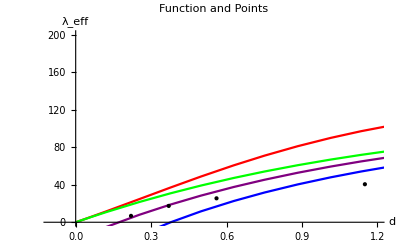

```mathematica
λ = 148;
l = 40*10^(-9);
K = 0.1;
Kmod =1;
KJou = 1;
Kso = 1;
m = 1;
mNet = 1;
α = 2/9;
α1 = 1/2;

JouPlot = Plot[condPltJou,{d,0, 620*10^(-9)},PlotStyle->Red];
correctedPlot = Plot[condPltNetHeatFlux,{d,0, 620*10^(-9)},PlotStyle->Yellow];
modPlot=Plot[condPltModNetHeatFlux,{d, 0, 620*10^(-9)},PlotStyle->Green];
SOPlot1 = Plot[condPltSOHeatFlux,{d, 0, 620*10^(-9)},PlotStyle->Purple];
SOPlot2 = Plot[condPltSOHeatFlux1,{d, 0, 620*10^(-9)},PlotStyle->Blue];

(*Define the points to be plotted*)
points={{22*10^(-9), 6.8}, {37*10^(-9),17.4},{56*10^(-9),25.5},{115*10^(-9),40.5}};
pointsPlot=ListPlot[points,PlotStyle->{Black,PointSize[Large]}];

(*Combine the function and the points*)
Show[{JouPlot, (*correctedPlot,*) modPlot, SOPlot1, SOPlot2},pointsPlot,PlotLabel->"Function and Points",AxesLabel->{"d","λ_eff"}, PlotRange -> {{-10*10^(-9),120*10^(-9)},{0, 200}}]
```

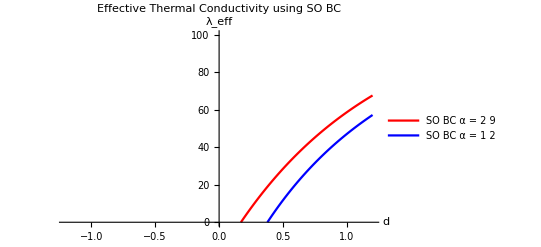

```mathematica
Plot[{condPltSOHeatFlux, condPltSOHeatFlux1},{d,0,120*10^(-9)},PlotLegends->{"SO BC α = 2
9",  "SO BC α = 1
2"},PlotStyle->{Red, Blue},AxesLabel->{"d","λ_eff"},PlotLabel->"Effective Thermal Conductivity using SO BC", PlotRange->{{-120*10^(-9),120*10^(-9)},{0, 100}}]
```

```mathematica
FindRoot[condPltSOHeatFlux==0,{d,2*10^(-9)}]
FindRoot[condPltSOHeatFlux1==0,{d,2*10^(-9)}]
```

{d→1.70708×10^-8}

{d→3.77892×10^-8}